# fiber AOM characterization

AOM A2.

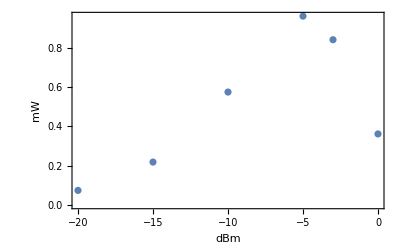

```mathematica
dBm={-20,-15,-10,-5,-3,0};(*the value entered in ARTIQ*)
mW={0.074,0.218,0.574,0.96,0.84,0.361};(*optical power measured with the Thorlabs free space power meter after the AOM*)
ListPlot[Transpose@{dBm,mW},Frame->{True,True},LabelStyle->Directive[Black,Medium],FrameLabel->{"dBm","mW"}]
```